```mathematica
Clear["Global`*"]
```

```mathematica
<<NDSolve`FEM`
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
a=1.0;
reg1=Rectangle[{0,0},{30,10}];
mesh=ToElementMesh[reg1,"MaxCellMeasure"->1,"MeshOrder"->1,"MeshElementType"->TriangleElement,"BoundaryMeshGenerator"->"RegionPlot"];
```

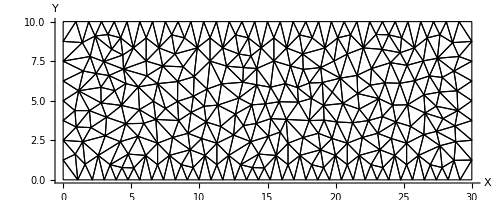

```mathematica
Show[mesh["Wireframe"],Axes->True,AxesLabel->{"X","Y"}]
```

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0.,(y==10.&&5.>x>0.)||(y==10.&&30.>x>25.)];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0.,(y==10.&&5.>x>0.)||(y==10.&&30.>x>25.)];
Subscript[Γ, Nv]=NeumannValue[-1.,16.>=x≥14.&&y==10.];
op1=op/.{Y->3000.,ν->0.33};
{state}=NDSolve`ProcessEquations[{op1=={0.,Subscript[Γ, Nv]},Subscript[Γ, Du],Subscript[Γ, Dv]},{u,v},{x,y}∈mesh];
femdata=state["FiniteElementData"];
pded=femdata["PDECoefficientData"];
bcd=femdata["BoundaryConditionData"];
md=femdata["FEMMethodData"];
sd=state["SolutionData"][[1]];
vd=state["VariableData"];
discretePDE=DiscretizePDE[pded,md,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
discreteBCs=DiscretizeBoundaryConditions[bcd,md,sd];
ele=DiscretizePDE[pded,md,sd,"SaveFiniteElements"->True];
{stiffnessElements,nonzeroPos}=ele["StiffnessElements"];
density=Table[ρ[i],{i,1,Length@stiffnessElements}];
modifiedElements=(density^1)*stiffnessElements;
Length@stiffnessElements
dof=md["DegreesOfFreedom"];
inci=Join@@md["Incidents"];
modifiedstiffness=AssembleMatrix[{inci,inci},modifiedElements,{dof,dof},"Sparse"->nonzeroPos];
displacement=Table[δ[i],{i,1,Length[stiffness]}];
coords=mesh["Coordinates"];
elems=mesh["MeshElements"];
DeployBoundaryConditions[{load,stiffness},discreteBCs];
DeployBoundaryConditions[{load,modifiedstiffness},discreteBCs];
loadF=mloadF=Flatten[load];
square=Join@@mesh["MeshElementMeasure"];
goalFunction=loadF.displacement;
massEquation=∑_(k=1)^Length[square] square⟦k⟧ density⟦k⟧≤(∑_(k=1)^Length[square] square⟦k⟧) 0.5;
densityEq=Thread[(0.≤#1≤1.&)[density]];
(*densityEq=(0.9≤#1≤1||0.0≤#1≤0.1)&/@density;*)
equation=Table[modifiedstiffness⟦i⟧.displacement==loadF⟦i⟧,{i,1,Length[displacement]}];
sysOfEq=Flatten[{goalFunction,massEquation,equation,densityEq}];
sysOfEq//Length;
variables=Flatten[{density,displacement}];
variables//Length;
initDis=Thread[{#,0}&[displacement]];
initDen=Thread[{#,0.5}&[density]];
initCond=Flatten[{initDen,initDis},1];
```

500

```mathematica
NMinimize[sysOfEq,variables,Method->"NelderMead"]
```

$Aborted

#### Darwinistic Algorithm

```mathematica
(*Seed the population*)
amount=30;
count=Length@stiffnessElements;
pop=RandomReal[{0,1},{amount,count}];
(*Crossover*)
cross[list1_List,list2_List]:=RandomChoice[{list1[[#]],list2[[#]]}]&/@Range[count];
geneData={};
mut:=RandomReal[{0.,0.5}];
mutn:=RandomInteger[{1,count},2];
```

```mathematica
For[k=1,k≤3000,k++,
(*Mutation*)
(*popn=RandomInteger[{1,amount}];*)
If[Divisible[RandomInteger[{1,5}],5],
For[n=1,n≤amount/2-1,n++,
{pop[[n+Floor[amount/2],mutn[[1]]]],pop[[n+Floor[amount/2],mutn[[2]]]]}={pop[[n+Floor[amount/2],mutn[[1]]]]+mut,pop[[n+Floor[amount/2],mutn[[1]]]]-mut};
];
];
(*Selection*)
rules=Thread[density->pop[[#]]]&/@Range[amount];

sel=Reap[
For[j=1,j≤amount,j++,
Evaluate[Table[ρ[i],{i,1,Length@stiffnessElements}]]=density/.rules[[j]];
sol=LinearSolve[modifiedstiffness,load];
Sow[Abs[Flatten[load].Flatten[sol]]];
Clear[ρ]
]
];

objpop=Transpose[{sel[[2,1]],pop}];
If[Divisible[k,10],Print[Min[sel[[2,1]]]]];
newpop=Transpose[TakeSmallestBy[objpop,First,Round[amount/2]]][[2]];
newpop=Select[newpop,Max[#]<=1.01&&Min[#]>0&];
newpop=((#/Mean[#])&/@newpop)*0.5;
newpop2=Apply[cross[#1,#2]&]/@Table[RandomChoice[newpop,2],amount-Length[newpop]];
pop=Join[newpop,newpop2];
AppendTo[geneData,pop];
]
```

```mathematica
newpop2//Length
```

```mathematica
geneData//Length
```

```mathematica
imagedata=Transpose[geneData][[1]];
animdata={};
```

```mathematica
For[i=1,i≤Length[imagedata],i=i+100,
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]]}&]/@elems[[1,1,1;;Length[square],1;;3]]);
maxden=Max[imagedata[[i]]];
denpolys=Transpose[{imagedata[[i]]/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
AppendTo[animdata,Graphics[opacityfiltered]];
]
```

```mathematica
ListAnimate[animdata,0.1]
```

```mathematica
(*Graphic*)
For[i=1,i≤Length[pop],i++,
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]]}&]/@elems[[1,1,1;;Length[square],1;;3]]);
maxden=Max[pop[[i]]];
denpolys=Transpose[{pop[[i]]/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
Print[Graphics[opacityfiltered]]
]
```

#### Artificial Immune Algorithm

```mathematica
(*Seed the population*)
amount=30;
count=Length@stiffnessElements;
pop=RandomReal[{0,1},{amount,count}];
```